===============================================================================

Dalam menjawab soal-soal berikut, saya mengasumsikan bahwa orang awam adalah orang-orang dengan kemampuan matematika yang cukup, yakni setidaknya memiliki pemahaman atas fungsi, turunan, dan integral serta berkeinginan untuk mempelajari atau menerapkan Wolfram Mathematica.

===============================================================================
===============================================================================

1. Gradien dari fungsi f dapat dicari dengan mencari turunan pertama dari f. Hal ini dapat divisualisasikan apabila fungsi f dan f’ mudah untuk digambarkan. Dengan menggunakan Wolfram Mathematica, buatlah Module fungsi dengan ketentuan sebagai berikut.
a. Nama fungsi Gradien[Parameter1, Parameter2]
b. Parameter1 adalah fungsi yang akan kita cari turunannya.
c. Parameter2 adalah sampai turunan sekian yang kita kehendaki.
d. Output dari fungsi ini adalah fungsi awal, turunan pertama, turunan kedua, sampai turunan kedua, sampai turunan ke-parameter2 (15 poin sampai tahap ini), beserta plot fungsinya dalam satu gambar (Poin penuh).
------------------------------------------------------------------------------------------------------------------------------------------
Mengenai soal ini, ada beberapa hal yang harus dimengerti terlebih dahulu, yaitu:
1. Cara membuat fungsi
2. Cara membuat fungsi yang memiliki parameter
3. Fungsi Module, For, Table, dan Plot serta Show
4. Clear

1. Cara membuat fungsi
Fungsi dibuat menggunakan “:=”
Misalkan:

```mathematica
x=2;
```

Dengan ini, kita telah mendefinisikan sebuah input x sebagai bernilai 2.
“;” berfungsi agar menjalankan program namun tidak menampilkan hasil.
Selanjutnya, kita akan buat contoh sebuah fungsi polinomial berisikan x:

```mathematica
P:=x^2+2x+1;
```

Dengan ini, kita telah membuat fungsi P.
Bila kita panggil fungsi P:

```mathematica
P
```

9

Maka kita akan dapatkan sesuai input nilai x yaitu 2 nilai P = 2^2+2*2+1= 4 + 4 + 1 = 9

2. Cara membuat fungsi yang memiliki parameter
Kita akan definisikan ulang fungsi yang sebelumnya menjadi P_1 dimana P_1 merupakan fungsi yang memiliki parameter:

```mathematica
Subscript[P, 1][x_]:=x^2+2x+1;
```

Parameter di sini memaksudkan bahwa saat kita panggil fungsi ini dengan menggantikan nilai parameternya sesuai input, akan muncul hasil yang diinginkan. Mari kita panggil fungsi ini dengan x = 2 seperti sebelumnya:

```mathematica
Subscript[P, 1][2]
```

9

Apa perbedaannya melakukan ini dengan cara yang sebelumnya?
Pada cara yang sebelumnya, kita terlebih dahulu harus mendefinisikan sebuah input x barulah mendefinisikan sebuah fungsi x yang nilainya digantikan oleh input x tersebut. Namun ini tidak efisien dikarenakan kita harus mendefinisikan ulang input x apabila ingin mengganti input x tersebut. Dengan fungsi yang langsung memetakan parameter x, maka hanya perlu memanggil fungsi beserta menggantikan parameter sesuai yang diinginkan, sehingga tidak perlu melakukan pendefinisian ulang input x kemudian kembali melakukan panggilan fungsi.

Suatu fungsi tidak terbatas pada satu parameter, namun bisa banyak parameternya. Sebagai contoh:

```mathematica
Subscript[P, 2][x_,y_,z_]:=(x+y-z)^2+2(x-y+z)-y-z;
```

Mari kita panggil fungsi ini dengan sembarang bilangan x, y, z. Misal x = 3, y = 2, z = 1

```mathematica
Subscript[P, 2][3,2,1]
```

17

Fungsi tersebut memetakan sesuai parameter dan mencari parameter tersebut dalam fungsi dan menggantikan nilainya dengan input.
Sesuai input: x = 3, y = 2, z = 1, maka yang bekerja dalam pemanggilan fungsi ini adalah:
(3 + 2 - 1)^2+2(3 - 2 + 1) - 2 - 1 = 4^2 + 2*2 - 3 = 16 + 4 - 3 = 17

3. Mengenai Fungsi Module, For, Table, dan Plot serta Show
- Fungsi Module adalah sebuah fungsi yang memungkinkan untuk melakukan fungsi-fungsi secara lokal.
Lokal di sini maksudnya adalah variabel dan fungsi yang ada pada lokal hanya bekerja secara internal.
Input x = 2 seperti sebelumnya merupakan Global.
Mungkin agak sulit untuk dimengerti dengan penjelasan seperti ini, maka perhatikan sebuah contoh berikut.
Misalkan G[x, y] sebuah fungsi yang akan menghasilkan output Jumlah dan Selisih dari x dan y.
Maka kita perlu membuat suatu Module dalam fungsi G[x, y] di mana parameternya adalah Jumlah dan Selisih.

```mathematica
G[x_,y_]:=
Module[
{Jumlah, Selisih},
Jumlah = x + y;
Selisih = Abs[x - y];
Print["Jumlah dari x dan y adalah: ", Jumlah];
Print["Selisih dari x dan y adalah: ", Selisih]
]
```

(catatan: Abs di sini berarti Absolute atau Mutlak. Mengapa demikian? Karena kita tidak mengetahui apakah nilai x atau y yang akan menjadi input yang lebih besar, maka karena kita mencari selisihnya di mana nilai selisih kita inginkan selalu bernilai tak negatif, maka kita gunakan fungsi mutlak atau Absolute)

Mari kita panggil fungsi ini dengan sembarang nilai x dan y, misal x = 2 dan y = 5.

```mathematica
G[2,5]
```

Jumlah dari x dan y adalah: 7

Selisih dari x dan y adalah: 3

Dengan contoh ini, dapat kita lihat bahwa Module memungkinkan kita untuk melakukan lebih dari 1 operasi dalam 1 fungsi. Selain efisien, hal ini akan menjadi efektif saat memerlukan sebuah fungsi yang menampilkan semua yang kita perlukan sekaligus.

- Fungsi For adalah fungsi iterasi yang melakukan pengulangan secara secara berurutsesuai step (naikan) yang kita definisikan untuk menghasilkan output secara berurut.
Sebagai contoh, kita akan buat sebuah fungsi yang mencetak (men-print) angka 1 hingga 5.

```mathematica
Prt :=For[i=1,i≤ 5,i++,Print[i]];
```

Fungsi tersebut dibaca sebagai: “Kita menset i sebagai 1. Maka selama i bernilai kurang lebih atau sama dengan 5 dengan step 1 (i++ berarti i = i + 1), maka akan di-print i.”
Mari kita jalankan fungsi tersebut.

```mathematica
Prt
```

1

2

3

4

5

For sangat berguna saat kita memerlukan melakukan pengulangan dalam suatu fungsi secara berurut.

- Fungsi Table adalah fungsi yang mengumpulkan output-outputnya menjadi satu.
Sebagai contoh, mari kita buat Table dari contoh sebelumnya yakni hasil 1 hingga 5:

```mathematica
Tbl:=Table[i,{i,1,5}];
```

Mari kita panggil fungsi ini.

```mathematica
Tbl
```

{1,2,3,4,5}

Fungsi Table akan berguna saat kita memerlukan menampilkan berbagai output.

- Fungsi Plot adalah fungsi yang membuat sketsa atau plotting dari suatu fungsi.
Sebagai contoh, mari kita sketsakan fungsi x^2:

```mathematica
Plt:=Plot[x^2,{x,-3,3},PlotRange->{0,10}];
```

Fungsi tersebut dibaca sebagai “Sketsakan x^2 dimana gambar difokuskan pada x di interval -3 hingga 3 dan pada y di interval 0 hingga 10”.
Mengapa y demikian? Karena x^2 selalu bernilai tak negatif.
Mari kita panggil fungsi tersebut.

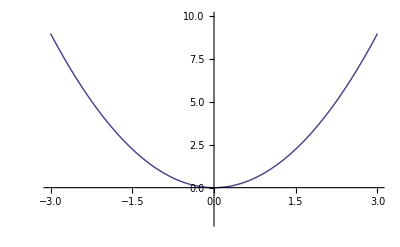

```mathematica
Plt
```

Apabila hanya begini saja, kurang menarik untuk dilihat.
Dapat dilakukan beberapa modifikasi terhadap plot sehingga akan tampak lebih enak dipandang.
Sebagai contoh, kita akan mengatur ketebalan atau Thickness menggunakan PlotStyle dan memberikan label pada fungsi tersebut menggunakan PlotLegends.

```mathematica
Plt1:=Plot[
x^2,{x,-3,3},
PlotRange->{0,10},
PlotStyle->Thickness[0.01],
PlotLegends->"Expressions"];
```

Mengenai Thickness, tidak ada cara pasti untuk menentukan sebuah angka agar ketebalan tepat sesuai yang diinginkan. Coba kreasikan saja berkali-kali hingga mendapatkan hasil yang diinginkan.
Mengenai Legends, Expressions merupakan salahsatu cara membubuhkan label. Ada beberapa cara seperti Automatic atau bahkan pengaturan penempatan. Baca saja documentationnya mengenai hal tersebut.
(Documentation merupakan alat yang sangat kuat karena dapat membantu menjadikan pekerjaanmu lebih maksimal. Documentation dapat diakses melalui Help > Documentation Center atau cara yang lebih enak adalah dengan mengetik suatu fungsi tidak sampai habis dan menklik tanda garis tiga yang akan muncul di sampingnya)

Sekarang mari kita panggil fungsi tersebut.

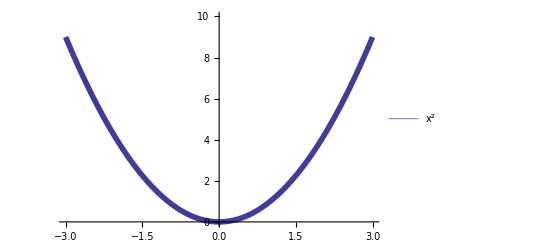

```mathematica
Plt1
```

Nah sekarang sudah lebih enak dilihat. Apabila ditunjukkan pada orang lain, mereka akan langsung paham bahwa disketsa sebuah grafik x^2 yang terlihat jelas karena telah ditebalkan.

- Fungsi Show adalah fungsi untuk memerlihatkan satu atau lebih grafik yang diciptakan melalui Plot atau Graphics. Sebagai contoh, kita dapat memerlihatkan fungsi sebelumnya dengan sebagai berikut:

```mathematica
Show[Plt1]
```

-Graphics-

4. Fungsi Clear
Sebelum kita beralih dari suatu pekerjaan ke pekerjaan lain, kita pasti telah menggunakan variabel-variabel yang kemungkinan akan bertabrakan dengan yang akan digunakan pada pekerjaan-pekerjaan berikutnya. Maka kita hilangan variabel tersebut menggunakan Clear.
Sebagai contoh, mari kita panggil x:

```mathematica
x
```

2

Maka apabila kita membuat fungsi yang melibatkan x, akan bertabrakan dengan input yang telah diberikan.
Maka kita akan hilangkan input nilai x dengan cara:

```mathematica
Clear[x]
```

Sekarang nilai x sudah tidak ada, apabila kita mencoba melakukan panggilan x:

```mathematica
x
```

x

Maka x sudah tidak bernilai.
-------------------------------------------------------------------------------------------------------------------------------------------------
Sekarang mari kita jawab soal nomor 1
-----------------------------------------------------
Pertama-tama, kita perlu mengidentifikasi parameter-parameter yang kita perlukan.
Yang kita perlu perhatikan, ada input-input global, yakni sebuah fungsi, katakan fungsi x dan berapa kali fungsi x ini diturunkan.
Maka kita dapatkan 2 buah parameter, yakni fungsi x, katakan f dan berapa kali diturunkan, katakan n.

Maka kita akan definisikan fungsi yakni Gradien[f, n]

Selanjutnya, apa sih yang kita perlukan dalam fungsi ini?
Kita akan perlukan sebuah list fungsi yang membuat daftar fungsi input beserta turunannya hingga n kali dan kita akan perlukan sebuah plotting yang memplot semua itu sekaligus agar menjadi satu plot terintegrasi.
Maka akan kita buat Module[{ListFungsi, GrafikFungsi}]

ListFungsi akan berisikan Table yang menghimpun input f dan turunannya hingga n kali. Maka kita akan buat fungsi For kemudian menggabungkannya dalam Table. Sebagai contoh suatu fungsi x^2+2x+3 diturunkan hingga 2 kali:

```mathematica
For[F=x^2+2x+3;Subscript[F, 0]=F;
i=1,i≤ 2,i++,Subscript[F, i]=D[F,{x,i}]
];

ListFungsi=Table[Subscript[F, i],{i,0,2}];
```

Fungsi For tersebut dibaca sebagai:
“Untuk F bernilai x^2+2x+3 dan F_0 bernilai F, kita men-set i sebagai 1 dan selama i kurang dari atau sama dengan 2 dengan step 1, maka F_i didefinisikan sebagai turunan F dengan ordo x sebanyak i kali.”

Sedangkan fungsi ListFungsi dibaca sebagai:
“Kita himpun output F_i pada interval i = 0 (mengapa? Karena i = 0, yakni F_0 adalah fungsi input. Target kita adalah menghimpun fungsi input beserta turunannya hingga 2 turunan) hingga i = 2.”

Mari kita jalankan fungsi tersebut.

```mathematica
ListFungsi
```

{3+2 x+x^2,2+2 x,2}

GrafikFungsi akan berisikan plotting dari ListFungsi pada suatu interval x dan suatu interval y.
Sebagai contoh, mari kita lakukan plotting pada ListFungsi yang telah kita definisikan sebelumnya.

```mathematica
GrafikFungsi=Plot[ListFungsi,{x,-3,3},PlotRange->{-12,12}];
```

Sekali lagi, interval-interval ini fleksibel, disesuaikan dengan input dan dicoba berkali-kali hingga sesuai yang diinginkan.
Mari kita jalankan fungsi tersebut.

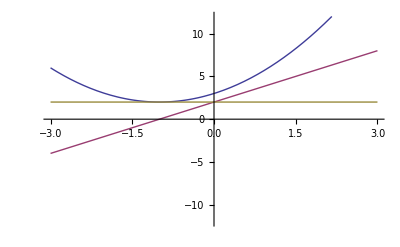

```mathematica
Show[GrafikFungsi]
```

-------------------------------------------------------------------------------------------------------------------------------------------------
Sekarang, mari kita buat fungsi lengkap untuk menjawab soal nomor 1 ini:

```mathematica
Gradien[f_,n_]:=
Module[
{ListFungsi,GrafikFungsi},

For[F=f;Subscript[F, 0]=F;
i=1,i≤ n,i++,Subscript[F, i]=D[F,{x,i}]
];

ListFungsi=Table[Subscript[F, i],{i,0,n}];

GrafikFungsi=Plot[ListFungsi,{x,-5,5},PlotRange->{-10,10}];

For[
i=0,i≤n,i++,
If[
i==0,
Print["Fungsi input: ", Subscript[F, i]],
Print["Fungsi turunan ke ", i, " dari fungsi input adalah: ", Subscript[F, i]]
]
];

Show[GrafikFungsi]
]
```

Fungsi input: 4-4 x+x^2+x^3

Fungsi turunan ke 1 dari fungsi input adalah: -4+2 x+3 x^2

Fungsi turunan ke 2 dari fungsi input adalah: 2+6 x

Fungsi turunan ke 3 dari fungsi input adalah: 6

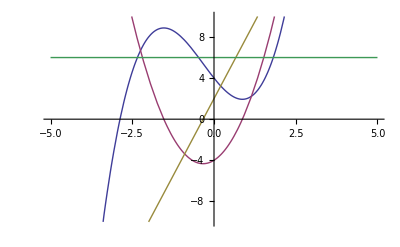

```mathematica
Gradien[x^3+x^2-4x+4,3]
```

Secara simpel, seperti itulah hasil yang kita dapatkan.
Namun jika ingin hasil yang lebih menarik, kita dapat sedikit kerjakan lebih lanjut seperti berikut:

```mathematica
Gradien[f_,n_]:=
Module[
{ListFungsi,GrafikFungsi},

For[F=f;Subscript[F, 0]=F;
i=1,i≤ n,i++,Subscript[F, i]=D[F,{x,i}]
];

ListFungsi=Table[Subscript[F, i],{i,0,n}];

GrafikFungsi=Plot[ListFungsi,{x,-5,5},PlotRange->{-10,10},
PlotStyle->Table[Thickness[i/(125*n)],{i,1,n}],
PlotLegends->SwatchLegend["Expressions",
LegendLabel->"Warna dan Fungsinya",
LegendFunction->(Framed[#,Background->Gray]&)]
]
;

For[
i=0,i≤n,i++,
If[
i==0,
Print["Fungsi input: ", Subscript[F, i]],
Print["Fungsi turunan ke ", i, " dari fungsi input adalah: ", Subscript[F, i]]
]
];

Print["
Sketsa grafik fungsi-fungsi yang dihasilkan: "]; Show[GrafikFungsi]
]
```

Fungsi input: 4-4 x+x^2+x^3

Fungsi turunan ke 1 dari fungsi input adalah: -4+2 x+3 x^2

Fungsi turunan ke 2 dari fungsi input adalah: 2+6 x

Fungsi turunan ke 3 dari fungsi input adalah: 6

Sketsa grafik fungsi-fungsi yang dihasilkan:

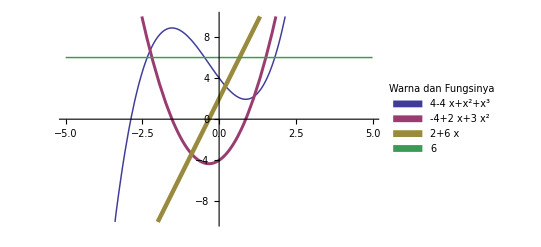

```mathematica
Gradien[x^3+x^2-4x+4,3]
```

Maka dengan ini, soal nomor 1 telah terjawab.
===============================================================================
===============================================================================

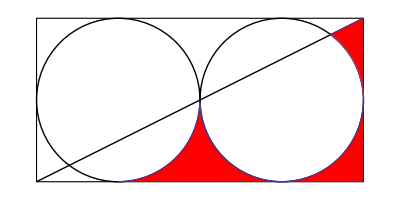
2. Hitunglah luas dari daerah yang diarsir menggunakan integral Monte Carlo
-Graphics-10
				20

------------------------------------------------------------------------------------------------------------------------------------------
Mari kita clear x dan n terlebih dahulu

```mathematica
Clear[x,n]
```

------------------------------------------------------------------------------------------------------------------------------------------
Untuk menjawab soal ini, kita harus dapat mendefinisikan fungsi-fungsi yang digunakan untuk membuat gambar tersebut.
Kita dapat melihat soal ini sebagai 7 fungsi, yakni:
1. 4 fungsi linear: x = 0, x = 20, y = 0, y = 10
2. 1 fungsi linear: y = 10/20x = x/2
3. 2 fungsi lingkaran 
(Ingat: Fungsi Lingkaran dapat kita tulis salahsatunya menggunakan (x-a)^2+(y-b)^2=r^2 dimana (a, b) = pusat lingkaran dan r = jari-jari lingkaran)
Perhatikan bahwa lingkaran ini memiliki jari-jari 5 dan lingkaran pertama berpusat pada (5, 5) dan lingkaran kedua berpusat pada (15, 5), maka
2 fungsi lingkaran tersebut: (x-5)^2+(y-5)^2=5^2 dan (x-15)^2+(y-5)^2=5^2

Ini merupakan fungsi mentah dari gambar tersebut dan akan diperbaiki fungsi-fungsi tersebut dalam menjawab soal.

------------------------------------------------------------------------------------------------------------------------------------------
Perhatikan gambar.
Perhatikan bahwa y=x/2 memotong lingkaran kedua pada 2 titik. Jelas bahwa titik pertama memotong pada x = 10 namun kita tidak mengetahui titik kedua memotong pada x berapa. Maka kita akan gunakan fungsi Solve, sebuah fungsi yang menyelesaikan 1 atau lebih persamaan untuk mendapatkan hasilnya.

```mathematica
Solve[y==x/2  && (x - 15)^2 + (y - 5)^2==25, {x,y}]
```

{{x→10,y→5},{x→18,y→9}}

Maka kita dapatkan titik potong yang kedua, yakni x = 18.

Sekarang kita akan definisikan fungsi-fungsi yang sesuai guna menjawab soal.
Kita akan 7 fungsi tersebut menjadi 3 fungsi utama:
Fungsi pertama (f1) adalah fungsi yang mengikuti lingkaran bawah melewati arsiran bagian atas hingga x = 20 dan y = 5,
Fungsi kedua (f2) adalah fungsi linear x/2, dan
Fungsi ketiga (f3) adalah fungsi yang mengikuti lingkaran bagian atas.

```mathematica
f1[x_]:=Piecewise[{{0,0≤ x<5},{5-√(25-(x-5)^2),5≤x<10},{5-√(25-(x-15)^2),10≤ x≤ 20}}];
f2[x_]:=x/2;
f3[x_]:=5+√(25-(x-15)^2);
```

(Piecewise merupakan fungsi yang mendefinisikan suatu fungsi berdasarkan pemecahan interval)

Sekarang kita akan melanjutkan dengan membuat gambar yang kita perlukan untuk menjawab soal.
Dapat menggunakan plot maupun graphics, namun dalam menjawab soal ini, akan digunakan graphics sehingga tidak ada garis koordinat kartesius agar gambar terlihat lebih rapi.

```mathematica
pic =Graphics[
{EdgeForm[{Thick,Black}],
White,Rectangle[{0,0},{20,10}],
Black,Circle[{5,5},5],
Black,Circle[{15,5},5],
Line[{{0,0},{20,10}}]
}
];
```

Fungsi EdgeForm memberikan batas pada border grafik yang dibuat
Fungsi Rectangle di sini membuat persegi panjang dari x = 0 hingga x = 20 dan dari y = 0 hingga y = 10
Fungsi Circle di sini yang pertama membuat lingkaran dengan pusat (5, 5) dan jari-jari 5
Fungsi Circle di sini yang kedua membuat lingkaran dengan pusat (15, 5) dan jari-jari 5
Fungsi Line di sini membuat sebuah garis lurus yang bermula dari titik (0,0) hingga titik (20,10)

Sekarang mari kita lihat gambar grafik yang kita buat.

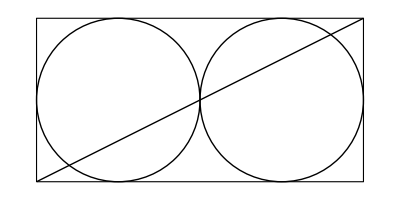

```mathematica
Show[pic]
```

Gambar ini masih kurang lengkap.
Gambar ini belum memiliki arsiran sebagaimana terlihat pada soal.
Maka kita akan buat arsiran tersebut.

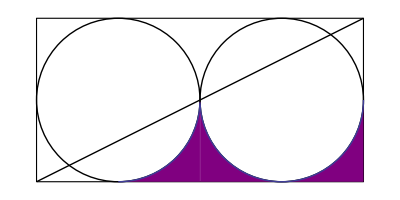

```mathematica
plt1=Plot[f1[x],{x,5,20},Filling->Axis,FillingStyle->Purple];
Show[pic,plt1]
```

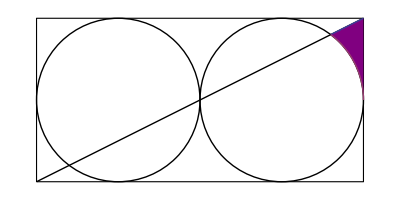

```mathematica
plt2=Plot[{f2[x],f3[x]},{x,18,20},Filling->{1->{2}},FillingStyle->Purple];
Show[pic,plt2]
```

Sekarang mari kita gabungkan kedua arsiran tersebut.

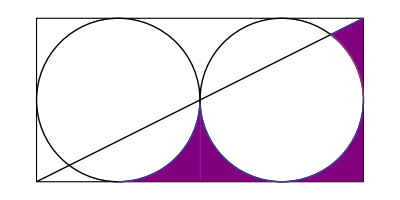

```mathematica
Show[pic, plt1, plt2]
```

Dengan ini, kita telah mendefinisikan fungsi-fungsi yang sesuai untuk menjawab soal ini.
Dan kita juga telah membuat gambar yang akan kita gunakan untuk menjawab soal ini.
Sebelum kita melangkah lebih lanjut, mari kita hitung jawaban dari soal ini secara eksak.

```mathematica
LuasAsli=N[∫_0^20 f1[x]ⅆx+∫_18^20 (f2[x]-f3[x])ⅆx]
```

19.5039

(N merupakan fungsi yang menampilkan hasil berbentuk bilangan desimal)
Dengan ini kita dapatkan target jawaban kita adalah 19.5039

Namun, perlu diingat, metode Monte Carlo merupakan approksimasi terhadap hasil.
Sehingga dalam menjawab soal ini, akan dispesifikasikan pula galat yang terjadi dalam pekerjaan ini.
-------------------------------------------------------------------------------------------------------------------------------------------------
Sekarang mari kita jawab soal nomor 2
-----------------------------------------------------

Akan dibuat sebuah fungsi MonteCarlo yang akan menampilkan banyaknya titik yang disebar dan luas berdasarkan metode monte carlo, kemudian luas aslinya, galatnya (untuk memerlihatkan efektivitas metode Monte Carlo terhadap metode menghitung luasnya secara eksak), beserta gambarnya dengan persebaran titik-titik yang digunakan.
MonteCarlo akan menggunakan sebuah parameter n, dimana n adalah banyaknya titik yang akan disebar dan digunakan.
Mengapa demikian? Mengapa tidak langsung membuat sebuah n yang tetap? Karena dengan begitu, kita dapat mengubah-ubah nilai n hingga mendapatkan n yang sesuai kebutuhan. n di sini tidak boleh terlalu kecil karena akan underfitting, yakni sampel akan terlalu dikit sehingga kemungkinan galat besar akan tinggi dan n tidak boleh terlalu besar karena akan overfitting, yakni sampel terlalu banyak sehingga titik akan terlalu banyak dan tidak memungkinkan kita melihat persebaran yang terjadi. Selain itu overfitting akan memakan biaya komputasi, yakni waktu komputasi karena semakin banyak titik yang disebar, maka waktu memprosesnya akan berjalan semakin lama.

Mari kita definisikan MonteCarlo[n]:

```mathematica
MonteCarlo[n_]:=
Module[
{RndX,RndY,ListTitik,Titik,LuasAppr,LuasAsli,Galat},

RndX=RandomReal[20,n];RndY=RandomReal[10,n];

plt1=Plot[f1[x],{x,5,20},Filling->Axis,FillingStyle->Purple];
plt2=Plot[{f2[x],f3[x]},{x,18,20},Filling->{1->{2}},FillingStyle->Purple];

pic=Graphics[
{EdgeForm[{Thick,Black}],
White,Rectangle[{0,0},{20,10}],
Black,Circle[{5,5},5],Circle[{15,5},5],
Line[{{0,0},{20,10}}]}
];

ListTitik=ListPlot[Table[{RndX[[i]],RndY[[i]]},{i,1,n}]];

For[i=1;t=0,i≤ n,i++,
If[RndX[[i]]≥  18,
If[RndY[[i]]≤  f1[RndX[[i]],t+=1],
If[
Or[RndY[[i]]≤  f1[RndX[[i]]]
],
And[RndY[[i]]≤  f2[RndX[[i]]]],
RndY[[i]]≥ f3[RndX[[i]]]]
t+=1]
]
]
;

LuasAsli=19.5039;

LuasAppr=N[(t*200)/n];

Galat=Abs[LuasAsli-LuasAppr];

Print[
"Jumlah titik yang disebar: ", n, " titik"
];
Print[
"Jumlah titik yang berada dalam daerah arsiran: ", t, " titik"
];
Print[
"Luas arsiran menggunakan metode Monte Carlo: ", LuasAppr, " satuan luas"
];
Print[
"Luas arsiran yang sebenarnya: ", LuasAsli, " satuan luas"
];
Print[
"
Galat metode Monte Carlo: ",Galat, " satuan luas"
];

Show[pic,plt1,plt2,ListTitik]
]
```

RandomReal adalah fungsi yang membuat nilai real acak, kemudian kita gunakan itu untuk mengevaluasi fungsi-fungsi terhadap arsiran.
LuasApproksimasi di sini menggunakan (t*200)/n, mengapa demikian? Karena kita menyebar dalam 200 satuan luas, yakni luas persegi panjang: 10 * 20.
Galat di sini menggunakan Abs karena kita tidak memerdulikan positif atau negatif. Kita hanya membutuhkan info seberapa jauh kesalahan luas approksimasi terhadap luas asli.

Kita telah mendefinisikan fungsi MonteCarlo. Mari kita tes menggunakan 3 jumlah titik, yakni 2000, 5000, dan 8000.

Jumlah titik yang disebar: 2000 titik

Jumlah titik yang berada dalam daerah arsiran: 210 titik

Luas arsiran menggunakan metode Monte Carlo: 21. satuan luas

Luas arsiran yang sebenarnya: 19.5039 satuan luas

Galat metode Monte Carlo: 1.4961 satuan luas

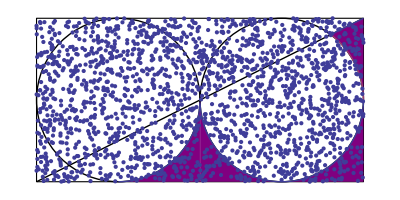

```mathematica
MonteCarlo[2000]
```

Tampak sangat enak dilihat, namun dengan persebaran titik sebanyak ini, kemungkinan mendapat galat yang masih cukup banyak masih cukup tinggi, maka kita akan coba titik yang lebih banyak.

Jumlah titik yang disebar: 5000 titik

Jumlah titik yang berada dalam daerah arsiran: 496 titik

Luas arsiran menggunakan metode Monte Carlo: 19.84 satuan luas

Luas arsiran yang sebenarnya: 19.5039 satuan luas

Galat metode Monte Carlo: 0.3361 satuan luas

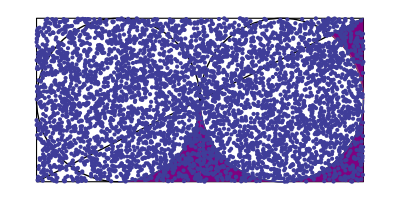

```mathematica
MonteCarlo[5000]
```

Tampaknya sudah bagus, titik yang digunakan sudah banyak namun kita masih dapat melihat dengan jelas.
Namun apakah sudah maksimal? Mari kita coba titik yang lebih banyak.

Jumlah titik yang disebar: 8000 titik

Jumlah titik yang berada dalam daerah arsiran: 799 titik

Luas arsiran menggunakan metode Monte Carlo: 19.975 satuan luas

Luas arsiran yang sebenarnya: 19.5039 satuan luas

Galat metode Monte Carlo: 0.4711 satuan luas

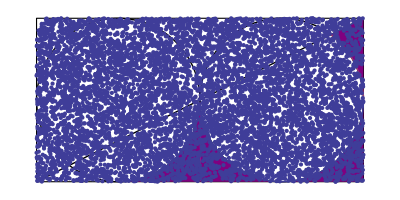

```mathematica
MonteCarlo[8000]
```

Ugh. Tampak sangat padat, hampir tak bisa melihat apa-apa.
Jika tidak menampilkan gambarnya, menggunakan banyaknya titik yang lebih besar ini akan lebih mengoptimalkan menghitung luas approksimasi, namun lebih baik jika kita menampilkan gambarnya pula agar orang lain mengerti apa yang kita maksud.

Maka berdasarkan contoh ini, kita dapat melihat bahwa kita harus memilih banyaknya titik dengan baik agar tidak underfitting maupun overfitting.

-------------------------------------------------------------------------------------------------------------------------------------------------
Sekarang, mari kita buat fungsi lengkap untuk menjawab soal nomor 1 ini:

```mathematica
MonteCarlo[n_]:=
Module[
{f1,f2,f3,pic, RndX,RndY,plt1,plt2,ListTitik,Titik,LuasAppr,LuasAsli,Galat},

f1[x_]:=Piecewise[{{0,0≤ x<5},{5-√(25-(x-5)^2),5≤x<10},{5-√(25-(x-15)^2),10≤ x≤ 20}}];
f2[x_]:=x/2;
f3[x_]:=5+√(25-(x-15)^2);

pic=Graphics[
{EdgeForm[{Thick,Black}],
White,Rectangle[{0,0},{20,10}],
Black,Circle[{5,5},5],Circle[{15,5},5],
Line[{{0,0},{20,10}}]}
];

RndX=RandomReal[20,n];RndY=RandomReal[10,n];

plt1=Plot[f1[x],{x,5,20},Filling->Axis,FillingStyle->Purple];
plt2=Plot[{f2[x],f3[x]},{x,18,20},Filling->{1->{2}},FillingStyle->Purple];

ListTitik=ListPlot[Table[{RndX[[i]],RndY[[i]]},{i,1,n}]];

For[i=1;t=0,i≤ n,i++,
If[RndX[[i]]≥  18,
If[RndY[[i]]≤  f1[RndX[[i]],t+=1],
If[
Or[RndY[[i]]≤  f1[RndX[[i]]]
],
And[RndY[[i]]≤  f2[RndX[[i]]]],
RndY[[i]]≥ f3[RndX[[i]]]]
t+=1]
]
]
;

LuasAsli=N[∫_0^20 f1[x]ⅆx+∫_18^20 (f2[x]-f3[x])ⅆx];

LuasAppr=N[(t*200)/n];

Galat=Abs[LuasAsli-LuasAppr];

Print[
"Jumlah titik yang disebar: ", n, " titik"
];
Print[
"Jumlah titik yang berada dalam daerah arsiran: ", t, " titik"
];
Print[
"Luas arsiran menggunakan metode Monte Carlo: ", LuasAppr, " satuan luas"
];
Print[
"Luas arsiran yang sebenarnya: ", LuasAsli, " satuan luas"
];
Print[
"
Galat metode Monte Carlo: ",Galat, " satuan luas"
];

Show[pic,plt1,plt2,ListTitik]
]
```

Jumlah titik yang disebar: 5000 titik

Jumlah titik yang berada dalam daerah arsiran: 478 titik

Luas arsiran menggunakan metode Monte Carlo: 19.12 satuan luas

Luas arsiran yang sebenarnya: 19.5039 satuan luas

Galat metode Monte Carlo: 0.383948 satuan luas

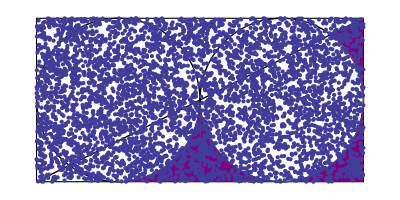

```mathematica
MonteCarlo[5000]
```

Maka dengan ini, soal nomor 2 telah terjawab.